# Regression

## Linear regression

### Model fitting

Imagine we have some data taken from an experiment and we would like to find a model that fits the data well.

Here is some data I took earlier. Can you figure out a good model for this data? Once you have a good idea for a model, try using Mathematica’s FindFit function to test it with the data. How would you verify that your model is a good fit for the data?

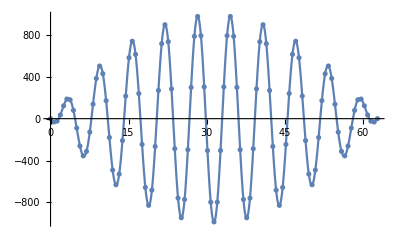

```mathematica
data=;
data;
Show[{ListPlot[data],Plot[(x^2-20 π x)Cos[x],{x,0,20 π}]}]
```

#### Analysis

Here is how I created that mystery data:

```mathematica
data = Table[{x,(x^2-20 π x) Cos[x]},{x,0,20 π, 20π/100}];
Iconize[data,"Mystery data"]
```

The first thing we should do is try to plot the data to see if we can recognise anything

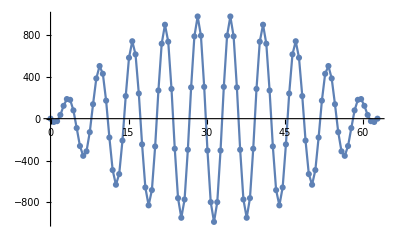

```mathematica
ListLinePlot[data,PlotMarkers->Automatic]
```

If we have a good idea for a model that might fit the data, then we can use FindFit to look for the parameters that best fit the data. This looks like the plot of cos(x) modulated by a quadratic so let’s try to fit a linear model of that form to the data:

```mathematica
model=(a1+a2 x+a3 x^2) Cos[x]/.FindFit[data,(a1+a2 x+a3 x^2) Cos[x],{a1,a2,a3},x]
```

(5.88143×10^-13-62.8319 x+1. x^2) Cos[x]

Now we plot the model against the data

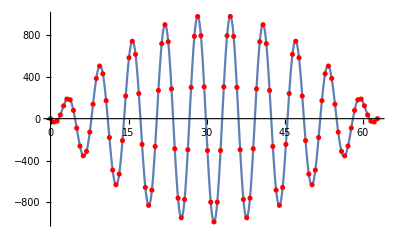

```mathematica
Show[Plot[model,{x,0,20 π}],ListPlot[data,PlotStyle->Red]]
```

Now that we have seen a simple example, let’s apply what we have learned in the lectures to see if we can reproduce this and in the process understand what Mathematica has done to find a good fit to the data.

### Linear Regression for a linear function

We will start with a simple problem: find the line that best fits some data by determining the best fit parameters (α, β) in our model f(x)=α+β x.

The first thing we need is to collect some data samples. Normally, this could come from some experimental measurements, but for this example we will just generate some data ourselves.  In the real world we will never have perfectly clean measurements so we will expect some random noise in our samples. To simulate this, we will add some random noise when we’re generating the data we want to fit.

```mathematica
data=Table[{x,3+2 x+RandomVariate[NormalDistribution[0,0.3]]},{x,0,5,0.5}];
MatrixForm[data]
```

(0. | 3.19971
0.5 | 4.6185
1. | 5.02403
1.5 | 6.29295
2. | 7.12349
2.5 | 8.22329
3. | 8.63429
3.5 | 10.0751
4. | 10.9317
4.5 | 11.9544
5. | 12.6296)

Now the first column are the values of x_i and the second column is f(x_i). Let’s extract those two columns from the matrix.

```mathematica
xi=data[[All,1]];
fxi=data[[All,2]];
```

The next thing we need to do is build up the matrix A representing our model evaluated for each value of x_i

```mathematica
A=Table[{1,x},{x,xi}];
MatrixForm[A]
```

(1 | 0.
1 | 0.5
1 | 1.
1 | 1.5
1 | 2.
1 | 2.5
1 | 3.
1 | 3.5
1 | 4.
1 | 4.5
1 | 5.)

```mathematica
MatrixForm[{α,β}]
```

(α
β)

Our model is then A(α
β)=f(x_i). The matrix A is an example where we have many rows but only two columns, so this is an over-constrained problem. As such we won’t be able to find a perfect solution (f(x_i) is not in the column space of A!), so we will look for a solutions that minimises ||A(α
β)=f(x_i)||. We saw how to do this in our linear algebra examples, where we had three ways to find the best fit solution:

#### Method 1: Directly minimise ||A(α β)=f(x_i)||

We can numerically search for the minimum over the parameters α and β. This is an example of an unconstrained convex optimisation problem

```mathematica
{min,sol}=FindMinimum[Norm[A.{α,β}-fxi]^2,{α,β}]
```

{0.402667,{α→3.36923,β→1.87802}}

We now check visually that we have indeed found the minimum:

```mathematica
Show[Plot3D[Norm[A.{α,β}-fxi]^2,{α,1,5},{β,1,3}],Graphics3D[Point[{3.23,1.93,Norm[A.{3.23,1.93}-fxi]^2}]]]
```

-Graphics3D-

This is equivalent to solving A^T A x̂=A^T f(x_i), i.e. using using A^Tto project onto the column space of A . Note that (A^T A)^-1 exists when A has independent columns [N(A) = N(A^T A)].

#### Method 2: QR

Recall that we saw that we could solve A^T A x̂=A^T f(x_i) efficiently if we had the QR decomposition of A. We have A^T A=(Q R)^T(QR) = R^T Q^T Q R=R^T R and A^T f(x_i)=(Q R)^T f(x_i)=R^T Q^T f(x_i) so our problem reduces to R x̂=Q^T b.

#### Method 3: Pseudoinverse

Our third approach is to use the pseudoinverse to solve the problem directly.

We could also this using the singular value decomposition

### Overfitting and under-fitting

We might think that we could obtain a better fit by introducing more parameters into our model. Similarly we might think that we could save some time by using fewer parameters. While this might be true in some cases, in many cases  it leads to problems of overfitting and under-fitting, respectively. Let’s use Mathematica’s Fit to fit three models to the data, one with too few parameters, one with two many, and one with the correct number

The green curve representing a 10th order polynomial certainly fits the blue points better (it exactly passes through them all - interpolation!) but it is clearly a worse fit than the orange. We have overfit our model. We could check for this by adding another point (which was not used in the training) and checking if it fits the model.

Similarly, the blue line (0th order polynomial) is an underfit and is not a good model for the data.

### Linear Regression for a nonlinear function (but still linear in parameters)

There is nothing in linear regression that assumes our model must be a liner function of the variables. Let’s try it with a nonlinear function

### Linear Regression in multiple dimensions

It is straightforward to generalise to data in multiple dimensions:

## Nonlinear regression

We haven’t covered it in the lectures, but we can also fit a non-linear model, where we have a non-linear function of the parameters. To start, let’s make up some data to use:

We can fit a nonlinear model to this data

Now we plot the model against the data to check it does fit

## Logistic regression

Finally, let’s look at an example of Logistic Regression. We will return to the MNIST Digits dataset we studied using Principal Component Analysis.

To save time, we will train the model using a subset of the data.

We could use LogitModelFit to fit a model and then used that to build a function that takes in an image and returns a number, but rather than worrying about the messy details we can use Classify with the LogisticRegression method specified. This takes care of converting the image to a matrix and all the other messy details.

We can now treat this as a function that takes in an image and returns a number. Let’s look at some information about the function:

Let’s see how well it performs by testing it on a random sample of the test data

It’s right about 2/3 of the time. We could improve this by going back to the training step and using more training samples:

Now this is close to 90% accurate